```mathematica
Clear["Global`"];
SetDirectory[NotebookDirectory[]];
(*Buttons to hide/show code*)CloseAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->False]&/@cells;];

OpenAllInputsCells[]:=Module[{nb,cells},nb=EvaluationNotebook[];
cells=Cells[nb,CellStyle->"Input"];
SetOptions[#,CellOpen->True]&/@cells;];

Row[{Button["Hide Code",SelectionEvaluate[CloseAllInputsCells[]]],Button["Show Code",SelectionEvaluate[OpenAllInputsCells[]]]}]
```

Hide CodeShow Code

```mathematica
settings=<|
aspectratio->1/3
,imagemargins->20
,imagesize->1000
,labelstyle->{14}
,origindate->"Sep. 14, 2011"
,plotbackground->Lighter[LightGray,0.75]
,plotmarkers->{None,{"OpenMarkers",8},{"OpenMarkers",8}}
,plotstyle->{Automatic,Darker[Green],Lighter[Red]}
,subtitlestyle -> {15}
,updatedstyle -> {12}
,ticksstyle->{16}
,titlestyle->{20,Red}
|>;
since=365*14;
prices = DeleteCases[Import["http://localhost:3110/api/vecs/dateindex-to-price-close?from=-10000"],Null];
max=Max[#]&/@prices;
min=Min[#]&/@prices;
mins=Table[
{Now - Quantity[x,"Days"],Min[Take[min,-x]]}
,{x,1,since,1}
]//Reverse;
maxs=Table[
{Now - Quantity[x,"Days"],Max[Take[Take[max,-since],since-x]]}
,{x,1,since,1}
]//Reverse;
(*closes=Take[#[[4]]&/@prices,-since];*)
(*close=Table[
{Now - Quantity[x,"Days"],closes[[since-x]]}
,{x,1,since,1}
]//Reverse;mavg=MovingAverage[Take[close,-days]//TimeSeries,200];*)
```

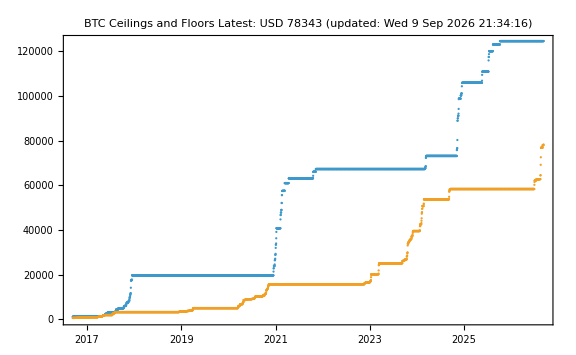

```mathematica
days=365*10;
updatedstr=Style[StringForm["(updated: ``)", DateString[]],settings[updatedstyle]];
DateListPlot[
{{
Take[maxs,-days]//TimeSeries
,Take[mins,-days]//TimeSeries
(*,Take[close,-days]//TimeSeries*)
}}
,FrameTicks->All
,GridLines->Automatic
,ImageSize->Large
,ImageMargins->20
,Joined->False
,PlotRange->Full
,PlotLabel->Column[
{
Style[
"BTC Ceilings and Floors"
,settings[titlestyle]
]
,Style[
"Latest: USD " <> ToString[Last[prices]//Round]
,settings[subtitlestyle]
]
,updatedstr
,Spacer[12]
}
,Center
]
]
```